# Learning tabular data

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

```mathematica
?neurallogic`*
```

## Get data

```mathematica
data=ResourceData["663653b1-6151-48ad-b693-3ee813b191c6"]
```

Dataset[<>]

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

## Create feature encoders

```mathematica
Encoders[data_]:=Block[{
features=Normal[Keys@First[data]],
featureValues
},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->NetEncoder[{"Class",Last[#],"IndicatorVector"}]&/@featureValues]
]
encoders=Encoders[trainData];
inputSize=Total[First[#["Output"]]&/@Normal/@Values[Drop[encoders,-1]]];
classes=Normal[DeleteDuplicates[data[All,"Acceptability"]]];
```

```mathematica
featureLayer=NetGraph[
<|
"Catenate"->CatenateLayer[]
|>,
Map[NetPort[First[#]]->"Catenate"&,Drop[Normal[encoders],-1]],
"PurchasePrice"->encoders["PurchasePrice"],
"MaintenanceCost"->encoders["MaintenanceCost"],
"Doors"->encoders["Doors"],
"Passengers"->encoders["Passengers"],
"Cargo"->encoders["Cargo"],
"Safety"->encoders["Safety"]
];
```

## Create net

```mathematica
{softNet,hardNet}=Block[{numClasses=Length[classes],classificationLayerSize},
classificationLayerSize=192*numClasses;
HardNeuralChain[{
HardNeuralNAND[inputSize,classificationLayerSize],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
net=NetGraph[<|"FeatureLayer"->featureLayer,"SoftNet"->softNet|>,{"FeatureLayer"->"SoftNet"}];
```

```mathematica
trainableNet=NetGraph[
<|"Net"->net,"Loss"->HardClassificationLoss[]|>,
{NetPort["Acceptability"]->NetPort["Loss","Target"],"Net"->"Loss"},
"Acceptability"->encoders["Acceptability"]
];
```

## Train net

```mathematica
result=NetTrain[trainableNet,trainData,All,
ValidationSet->RandomSample[testData,UpTo[1000]],
LossFunction->"Loss",
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

## Evaluate soft net

```mathematica
trainedSoftNet=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[result["TrainedNet"]],"Loss/Error"]|>,
{},"Output"->NetDecoder[encoders["Acceptability"]]
];
```

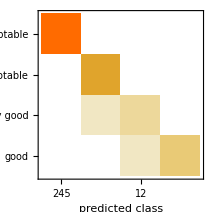
Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (99.40.4) %
Accuracy baseline | (70.82.4) %
Geometric mean of probabilities | 0.965 ± 0.0074
Mean cross entropy | 0.0352 ± 0.0076
Single evaluation time | 4.61 ms/example
Batch evaluation speed | 2.91 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[trainedSoftNet,testData->"Acceptability"]
```

## Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedSoftNet];
be=HardNetBooleanExpression[hnf,inputSize];
bf=HardNetBooleanFunction[hnf,inputSize];
```

```mathematica
hncwt=HardNetClassify[bf,featureLayer,NetDecoder[encoders["Acceptability"]],testData,"Acceptability"];
eval=HardNetClassifyEvaluation[hncwt]
```

<|Accuracy→0.991329|>

```mathematica
MapIndexed[{#2[[1]],trainedSoftNet[Drop[#1,-1],"Probabilities"],HardNetClassProbabilities[HardNetClassScores[HardNetClassBits[bf,featureLayer,{Drop[#1,-1]}]]]}&,testData]
```

```mathematica
testData[[308]]
```

```mathematica
{trainedSoftNet[Drop[#1,-1],"Probabilities"],HardNetClassProbabilities[HardNetClassScores[HardNetClassBits[bf,featureLayer,{Drop[#1,-1]}]]]}&/@{testData[[308]]}
```

{{,{{0.999089,0.000911051,1.26526×10^-14,1.38753×10^-11}}}}

```mathematica
HardNetClassScores[HardNetClassBits[bf,featureLayer,{Drop[testData[[308]],-1]}]]
```

{{75,75,50,53}}